```mathematica
Clear[f]
f[x_]:=x+3/x
```

```mathematica
Clear[tanLine]
tanLine[{a_,b_}]:=(f[b]-f[a])/(b-a)
```

```mathematica
Clear[EqTanline]
EqTanline[{a_,b_},x_]:=Module[{},
f'[Flatten[Solve[f'[x]==tanLine[{a,b},x],x]][[2]]](x-a)]
```

```mathematica
EqTanline[{1,6},x]
```

(1-3/x^2) (-1+x)

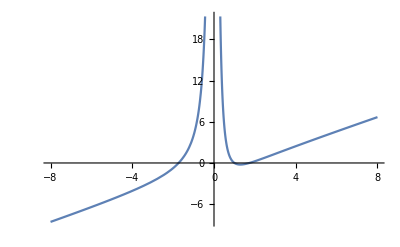

```mathematica
Plot[(1-3/x^2) (-1+x),{x,-8,8}]
```

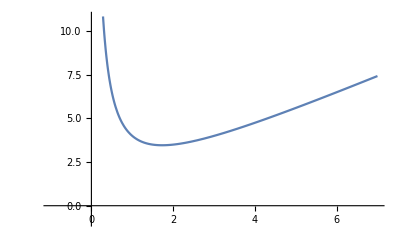

```mathematica
Plot[{f[x],tanLine[{1,6},x]x,EqTanline[{1,6},x]},{x,-1,7}]
```

```mathematica
Solve[f'[x]==tanLine[{1,6}],x]
```

{{x→-√6},{x→√6}}